Andrea Halenkamp
MAT 325
4/21/2017

# Final Project

## Part I: Analyze the Predator Prey System

System:
	x’ = 2 x - x * y
	y’ = -(1/2) y + x * y
Assume the prey are insects.

### Find the equilibrium points by graphing the nullclines and using Mathematica to Solve for the equilibrium points.

Graph of nullclines, intersections are equilibrium points.

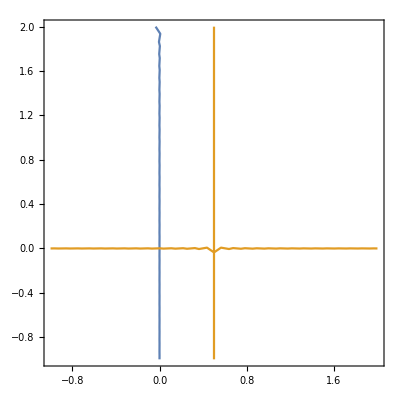

```mathematica
ContourPlot[{2x-x*y==0,-(1/2)*y+x*y==0},{x,-1,2},{y,-1,2}]
```

Solve for each equation equaling zero in order to get nullclines.

```mathematica
Solve[{2x-x*y==0,-(1/2)*y+x*y==0},{x,y}]
```

{{x→0,y→0},{x→1/2,y→2}}

### Calculate the Jacobian Matrix.

Create the functions within Mathematica as f[x,y] and g[x,y].

```mathematica
f[x_,y_]:=2x-x*y;
g[x_,y_]:=-(1/2)*y+x*y;
```

Calculate the Jacobian Matrix.

```mathematica
j[x_,y_]={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}
```

{{2-y,-x},{y,-1/2+x}}

### For each critical point, evaluate the Jacobian at the point, find the eigenvalues, find the eigenvectors, and classify the equilibrium point. If the real part of the eigenvalue is 0, then state that you are not able to classify the equilibrium point.

#### Classify (0, 0): Saddle (unstable)

Evaluate the Jacobian Matrix at point (0,0).

```mathematica
j[0,0]
```

{{2,0},{0,-1/2}}

```mathematica
Eigensystem[j[0,0]]
```

{{2,-1/2},{{1,0},{0,1}}}

#### Classify (1/2, 2): Center (stable)

```mathematica
j[1/2,2]
```

{{0,-1/2},{2,0}}

```mathematica
Eigensystem[j[1/2,2]]
```

{{ⅈ,-ⅈ},{{ⅈ/2,1},{-ⅈ/2,1}}}

```mathematica
f[1/2,3]
```

-1/2

### Draw Phase Portrait.

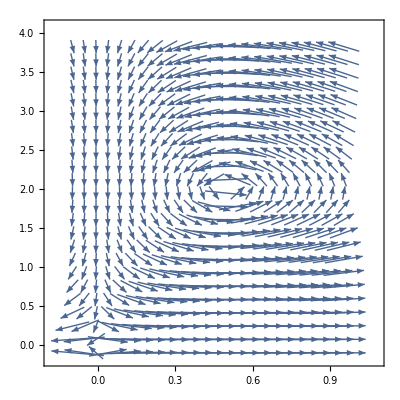

```mathematica
VectorPlot[{2x-x*y,-(1/2)*y+x*y},{x,-0.1,1},{y,-0.1,4},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine]
```

```mathematica
Clear[f,g,j];
```

## Part II: Introduce insecticide that kills both predators and prey

New System:
	x’ = 2 x - x - x * y
	y’ = -(1/2) y - y + x * y

### Find the equilibrium points by graphing the nullclines and using Mathematica to Solve for the equilibrium points.

Graph of nullclines, intersections are equilibrium points.

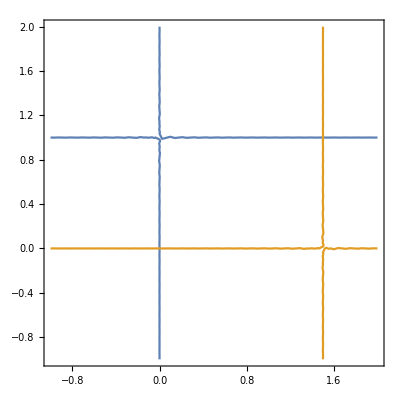

```mathematica
ContourPlot[{2x-x-x*y==0,-(1/2)*y-y+x*y==0},{x,-1,2},{y,-1,2}]
```

Solve for each equation equaling zero in order to get nullclines.

```mathematica
Solve[{2x-x-x*y==0,-(1/2)*y-y+x*y==0},{x,y}]
```

{{x→0,y→0},{x→3/2,y→1}}

### Calculate the Jacobian Matrix.

Create the functions within Mathematica as f[x,y] and g[x,y].

```mathematica
f[x_,y_]:=2x-x-x*y;
g[x_,y_]:=-(1/2)*y-y+x*y;
```

Calculate the Jacobian Matrix.

```mathematica
j[x_,y_]={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}
```

{{1-y,-x},{y,-3/2+x}}

### For each critical point, evaluate the Jacobian at the point, find the eigenvalues, find the eigenvectors, and classify the equilibrium point. If the real part of the eigenvalue is 0, then state that you are not able to classify the equilibrium point.

#### Classify (0, 0): Saddle (unstable)

Evaluate the Jacobian Matrix at point (0,0).

```mathematica
j[0,0]
```

{{1,0},{0,-3/2}}

```mathematica
Eigensystem[j[0,0]]
```

{{-3/2,1},{{0,1},{1,0}}}

#### Classify (3/2, 1): Center (stable)

```mathematica
j[3/2,1]
```

{{0,-3/2},{1,0}}

```mathematica
Eigensystem[j[3/2,1]]
```

{{ⅈ √(3/2),-ⅈ √(3/2)},{{ⅈ √(3/2),1},{-ⅈ √(3/2),1}}}

### Draw Phase Portrait.

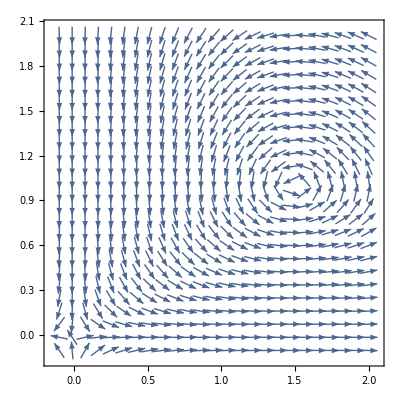

```mathematica
VectorPlot[{2x-x-x*y,-(1/2)*y-y+x*y},{x,-0.1,2},{y,-0.1,2},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine]
```

```mathematica
Clear[f,g,j];
```